```mathematica
r = (γ*λ)/4*(λ1+s)/((λ1+s)^2-β^2*(λ1+I*ω0)^2)
```

(γ λ (s+λ1))/(4 ((s+λ1)^2-β^2 (λ1+ⅈ ω0)^2))

```mathematica
r1 = 1/(s+r+I*d)(*正的那一个*)
```

1/(ⅈ d+s+(γ λ (s+λ1))/(4 ((s+λ1)^2-β^2 (λ1+ⅈ ω0)^2)))

```mathematica
r2 = r1/.{ω0->1.5*10^9,λ->1,d->0.3,λ1->1}
```

1/((0.+0.3 ⅈ)+s+((1+s) γ)/(4 ((1+s)^2+(2.25×10^18-3.×10^9 ⅈ) β^2)))

```mathematica
Mp = InverseLaplaceTransform[r2,s,t];
```

```mathematica
MpB3 = Mp/.{β->3*10^(-9),γ->0.1};
```

```mathematica
rr1 = 1/(s+r-I*d)(*负的那一个*)
```

1/(-ⅈ d+s+(γ λ (s+λ1))/(4 ((s+λ1)^2-β^2 (λ1+ⅈ ω0)^2)))

```mathematica
rr2 = rr1/.{ω0->1.5*10^9,λ->1,d->0.3,λ1->1}
```

1/((0.-0.3 ⅈ)+s+((1+s) γ)/(4 ((1+s)^2+(2.25×10^18-3.×10^9 ⅈ) β^2)))

```mathematica
Mm = InverseLaplaceTransform[rr2,s,t];
```

```mathematica
MmB3 =  Mm/.{β->3*10^(-9),γ->0.1};
```

```mathematica
c1B3 = 1/2*(MpB3+MmB3);
c2B3 = 1/2*(MpB3-MmB3);
```

```mathematica
EbB3 = ComplexExpand[Abs[c2B3]^2];
(*开始计算beta=0的值，mathematical计算的好快*)
MpB0 =  Mp/.{β->0,γ->0.1};
MmB0 =  Mm/.{β->0,γ->0.1};
c1B0 = 1/2*(MpB0+MmB0);
c2B0 = 1/2*(MpB0-MmB0);
EbB0 = ComplexExpand[Abs[c2B0]^2];(*前面的omega0就不乘了，反正最后都得除掉*)
```

```mathematica
MpB8 =  Mp/.{β->8*10^-9,γ->0.1};
MmB8 =  Mm/.{β->8*10^-9,γ->0.1};
c1B8 = 1/2*(MpB8+MmB8);
c2B8 = 1/2*(MpB8-MmB8);
EbB8 = ComplexExpand[Abs[c2B8]^2];(*前面的omega0就不乘了，反正最后都得除掉*)
```

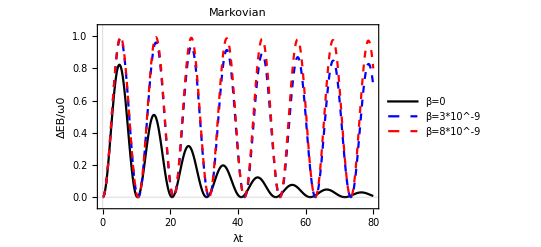

```mathematica
Plot[{EbB0,EbB3,EbB8},{t,0,80},PlotLegends->{"β=0","β=3*10^-9","β=8*10^-9"},PlotStyle->{Directive[Black,Thick],Directive[Blue,Dashed,Thick],Directive[Red,Dashed,Thick]},PlotRange->{-0.05,1.05},PlotTheme->"Scientific",FrameStyle->Directive[Black,Thick],FrameLabel->{"λt","ΔEB/ω0"},PlotLabel->"Markovian"]
```

```mathematica
(*==================开始绘制强耦合的情况===========================*)
```

```mathematica
MpBB0 =  Mp/.{β->0,γ->20};
MmBB0 =  Mm/.{β->0,γ->20};
c1BB0 = 1/2*(MpBB0+MmBB0);
c2BB0 = 1/2*(MpBB0-MmBB0);
EbBB0 = ComplexExpand[Abs[c2BB0]^2];
MpBB3 =  Mp/.{β->3*10^-9,γ->20};
MmBB3 =  Mm/.{β->3*10^-9,γ->20};
c1BB3 = 1/2*(MpBB3+MmBB3);
c2BB3 = 1/2*(MpBB3-MmBB3);
EbBB3 = ComplexExpand[Abs[c2BB3]^2];
MpBB8 =  Mp/.{β->8*10^-9,γ->20};
MmBB8 =  Mm/.{β->8*10^-9,γ->20};
c1BB8 = 1/2*(MpBB8+MmBB8);
c2BB8 = 1/2*(MpBB8-MmBB8);
EbBB8 = ComplexExpand[Abs[c2BB8]^2];
```

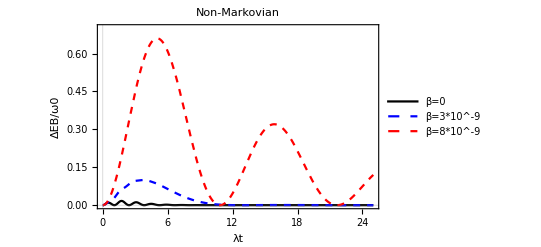

```mathematica
Plot[{EbBB0,EbBB3,EbBB8},{t,0,25},PlotLegends->{"β=0","β=3*10^-9","β=8*10^-9"},PlotStyle->{Directive[Black,Thick],Directive[Blue,Dashed,Thick],Directive[Red,Dashed,Thick]},PlotRange->{0,0.7},PlotTheme->"Scientific",FrameStyle->Directive[Black,Thick],FrameLabel->{"λt","ΔEB/ω0"},PlotLabel->"Non-Markovian"]
```

```mathematica
(*计算β=7e-9，γ=0.1也就是弱耦合的情况下*)
MpA7 =  Mp/.{β->7*10^-9,γ->0.1};
MmA7 =  Mm/.{β->7*10^-9,γ->0.1};
c1A7 = 1/2*(MpA7+MmA7);
c2A7 = 1/2*(MpA7-MmA7);
EA7 = ComplexExpand[Abs[Abs[c1A7]^2-1]];
```

```mathematica
MpB7 =  Mp/.{β->7*10^-9,γ->0.1};
MmB7 =  Mm/.{β->7*10^-9,γ->0.1};
c1B7 = 1/2*(MpB7+MmB7);
c2B7 = 1/2*(MpB7-MmB7);
EbB7 = ComplexExpand[Abs[c2B7]^2];
```

```mathematica
(*计算β=0*)
MpA0 =  Mp/.{β->0,γ->0.1};
MmA0 =  Mm/.{β->0,γ->0.1};
c1A0 = 1/2*(MpA0+MmA0);
c2A0 = 1/2*(MpA0-MmA0);
EA0 = ComplexExpand[Abs[Abs[c1A0]^2-1]];
```

```mathematica
Plot[{EbB0,EbB7,EA0,EA7},{t,0,80},PlotLegends->{"ΔE_B for β=0","ΔE_B for β=7*10^-9","|ΔE_A|for β=0","|ΔE_A|for β=7*10^-9"},PlotStyle->{Directive[Black,Thick],Directive[Blue,Dashed,Thick],Directive[Green,Dashed,Thick],Directive[Red,Dashed,Thick]},PlotRange->{-0.05,1.05},PlotTheme->"Scientific",FrameStyle->Directive[Black,Thick],FrameLabel->{"λt","ΔE_B/ω_0&|ΔE_A|"},PlotLabel->"Markovian"]
```

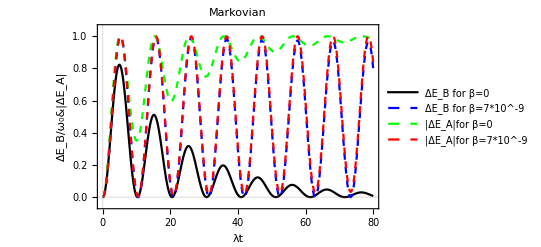
```mathematica
-Graphics-(*开放的量子电池最终应该都能达到一个稳态这里的一直在震荡，所以按理来说应该是可以用非互易的那套，但是这个时候用的是qubit而不是谐振子，有点难*)(*从左边的图可以看出来，当电池和充电器的量子比特具有一定的速度的时候，充电器的能量几乎完全的转换到了电池中，而没有向外界耗散*)
```

```mathematica
(*计算β=7e-9，γ=20也就是强耦合的情况下*)
MpAA7 =  Mp/.{β->7*10^-9,γ->20};
MmAA7 =  Mm/.{β->7*10^-9,γ->20};
c1AA7 = 1/2*(MpAA7+MmAA7);
c2AA7 = 1/2*(MpAA7-MmAA7);
EAA7 = ComplexExpand[Abs[Abs[c1AA7]^2-1]];
```

```mathematica
MpBB7 =  Mp/.{β->7*10^-9,γ->20};
MmBB7 =  Mm/.{β->7*10^-9,γ->20};
c1BB7 = 1/2*(MpBB7+MmBB7);
c2BB7 = 1/2*(MpBB7-MmBB7);
EbBB7 = ComplexExpand[Abs[c2BB7]^2];
(*计算β=0*)
MpA0 =  Mp/.{β->0,γ->20};
MmA0 =  Mm/.{β->0,γ->20};
c1A0 = 1/2*(MpA0+MmA0);
c2A0 = 1/2*(MpA0-MmA0);
EAA0 = ComplexExpand[Abs[Abs[c1A0]^2-1]];
```

```mathematica
Plot[{EbBB0,EbBB7,EAA0,EAA7},{t,0,30},PlotLegends->{"ΔE_B for β=0","ΔE_B for β=7*10^-9","|ΔE_A|for β=0","|ΔE_A|for β=7*10^-9"},PlotStyle->{Directive[Black,Thick],Directive[Red,Dashed,Thick],Directive[Green,Dashed,Thick],Directive[Blue,Dashed,Thick]},PlotRange->{-0.05,1.05},PlotTheme->"Scientific",FrameStyle->Directive[Black,Thick],FrameLabel->{"λt","ΔE_B/ω_0&|ΔE_A|"},PlotLabel->"Markovian"]
```

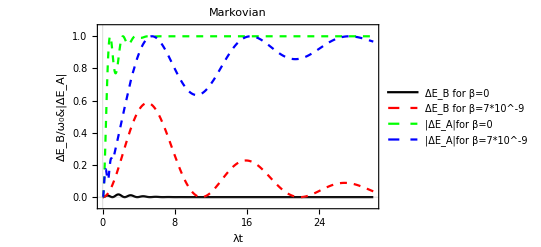
```mathematica
-Graphics-(*从上面的图中可以看到，在强耦合的情况下，充电器中的能量有很多大一部分耗散到环境中去了，而且这还是在电池和充电器都在运动的情况下，如果电池和充电器都静止的情况下，充电器中的能量基本上都耗散到环境中去了。*)
```

```mathematica
(*下面画最大可提取功的图像，其实也就是容易的很*)
```

```mathematica
erB0=(2*ComplexExpand[Abs[c2B0]^2]-1)*HeavisideTheta[ComplexExpand[Abs[c2B0]^2-1/2]];
erB3 =(2*ComplexExpand[Abs[c2B3]^2]-1)*HeavisideTheta[ComplexExpand[Abs[c2B3]^2-1/2]];
erB8 =(2*ComplexExpand[Abs[c2B8]^2]-1)*HeavisideTheta[ComplexExpand[Abs[c2B8]^2-1/2]];
```

```mathematica
Plot[{erB0,erB3,erB8},{t,0,80},PlotLegends->{"β=0","β=3*10^-9","β=8*10^-9"},PlotStyle->{Directive[Black,Thick],Directive[Blue,Dashed,Thick],Directive[Red,Dashed,Thick]},PlotRange->{-0.05,1.05},PlotTheme->"Scientific",FrameStyle->Directive[Black,Thick],FrameLabel->{"λt","W_B/W_max"},PlotLabel->"Markovian   &    Fig4a"]
```

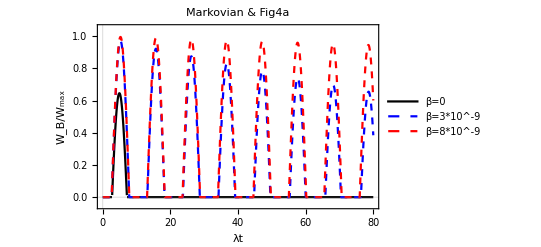
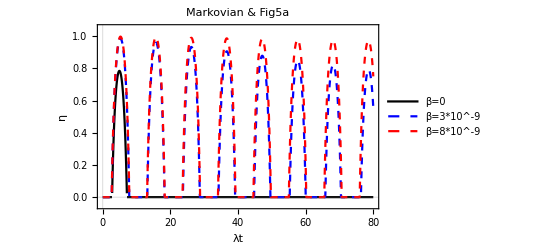

```mathematica
erBB0=(2*ComplexExpand[Abs[c2BB0]^2]-1)*HeavisideTheta[ComplexExpand[Abs[c2BB0]^2-1/2]];
erBB3 =(2*ComplexExpand[Abs[c2BB3]^2]-1)*HeavisideTheta[ComplexExpand[Abs[c2BB3]^2-1/2]];
erBB8 =(2*ComplexExpand[Abs[c2BB8]^2]-1)*HeavisideTheta[ComplexExpand[Abs[c2BB8]^2-1/2]];
```

```mathematica
Plot[{erBB0,erBB3,erBB8},{t,0,15.5},PlotLegends->{"β=0","β=3*10^-9","β=8*10^-9"},PlotStyle->{Directive[Black,Thick],Directive[Blue,Dashed,Thick],Directive[Red,Dashed,Thick]},PlotRange->{-0.05,0.35},PlotTheme->"Scientific",FrameStyle->Directive[Black,Thick],FrameLabel->{"λt","W_B/W_max"},PlotLabel->"Non-Markovian    &     Fig4b"]
```

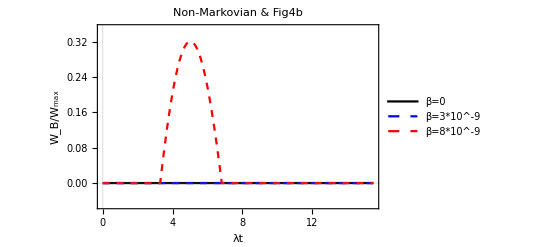
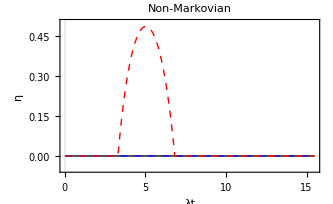

```mathematica
(*画η*)
ηB0 = erB0/EbB0;
ηB3 = erB3/EbB3;
ηB8 = erB8 / EbB8;
Plot[{ηB0,ηB3,ηB8},{t,0,80},PlotLegends->{"β=0","β=3*10^-9","β=8*10^-9"},PlotStyle->{Directive[Black,Thick],Directive[Blue,Dashed,Thick],Directive[Red,Dashed,Thick]},PlotRange->{-0.05,1.05},PlotTheme->"Scientific",FrameStyle->Directive[Black,Thick],FrameLabel->{"λt","η"},PlotLabel->"Markovian     &     Fig5a"]
```

-Graphics-

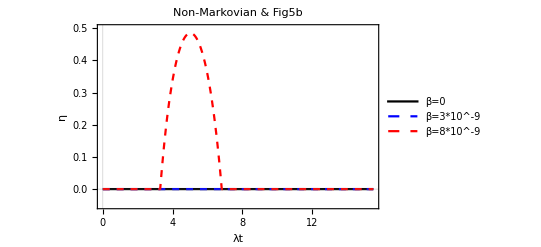

```mathematica
ηBB0 = erBB0/EbBB0;
ηBB3 = erBB3/EbBB3;
ηBB8 = erBB8 / EbBB8;
Plot[{ηBB0,ηBB3,ηBB8},{t,0,15.5},PlotLegends->{"β=0","β=3*10^-9","β=8*10^-9"},PlotStyle->{Directive[Black,Thick],Directive[Blue,Dashed,Thick],Directive[Red,Dashed,Thick]},PlotRange->{-0.05,0.5},PlotTheme->"Scientific",FrameStyle->Directive[Black,Thick],FrameLabel->{"λt","η"},PlotLabel->"Non-Markovian    &    Fig5b"]
```

```mathematica
Mpb3 =  Mp/.{β->3*10^-9,γ->10};
Mmb3 =  Mm/.{β->3*10^-9,γ->10};
c1b3 = 1/2*(Mpb3+Mmb3)*Sqrt[1/2]+1/2*(Mpb3-Mmb3)*Sqrt[1/2];
c2b3 =1/2*(Mpb3+Mmb3)*Sqrt[1/2]+1/2*(Mpb3-Mmb3)*Sqrt[1/2];
dd3 = -ComplexExpand[Log[ComplexExpand[Abs[(c1b3*ComplexExpand[Conjugate[c2b3]])*2]]]];
```

```mathematica
Mpb0 =  Mp/.{β->0,γ->10};
Mmb0 =  Mm/.{β->0,γ->10};
c1b0 = 1/2*(Mpb0+Mmb0)*Sqrt[1/2]+1/2*(Mpb0-Mmb0)*Sqrt[1/2];
c2b0 =1/2*(Mpb0+Mmb0)*Sqrt[1/2]+1/2*(Mpb0-Mmb0)*Sqrt[1/2];
dd0 =-ComplexExpand[Log[ComplexExpand[Abs[ (c1b0*ComplexExpand[Conjugate[c2b0]])*2]]]];
```

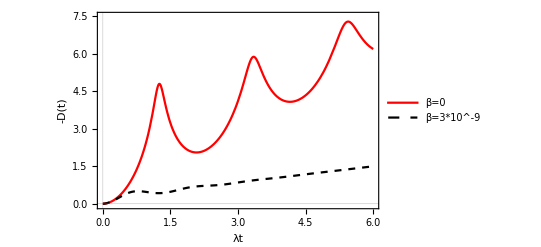

```mathematica
Plot[{dd0,dd3},{t,0,6},PlotLegends->{"β=0","β=3*10^-9"},PlotRange->{-0.05,7.5},PlotStyle->{Directive[Red,Thick],Directive[Black,Dashed,Thick]},PlotTheme->"Scientific",FrameStyle->Directive[Black,Thick],FrameLabel->{"λt","-D(t)"}]
```

```mathematica
Log[E]
```

1